This notebook implements a Qantum Anomalous Hall Insulator on a square lattice with a dislocation center, and the projected brane also contains the dislocation center.

Then exports the eigenspectrum to a .dat file

The .dat files generated with this notebook are plotted with EnergySpectra_QAHI_dislocation.nb

```mathematica
tStart = AbsoluteTime[];
```

```mathematica
Clear[Lx, Ly, A, l, mL,
 SX2DSingDis,SY2DSingDis,
 CX2DSingDis,CY2DSingDis,
SX2DPSingDis,CX2DPSingDis,
 Cons]
```

```mathematica
(** Change Lx, Ly and m in the following lines before running the code **)
```

```mathematica
(** we will set t = 1 = 2 t0. **)
```

```mathematica
Lx =60;
Ly = 60;
l = Ly/2;
mL = Lx/2;
A = Lx*Ly + Ly-l
NOrbitals = 2*A;
t=1;
t0 = 0.5;
m=6*t0;
```

410

```mathematica
(**-----------------Define the sine and cosine matrices for the parent square lattice with dislocation center--------------------**)
```

```mathematica
(**------------------------------------**)
```

```mathematica
SX2DSingDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{SX2DSingDis[[a + b Lx, a + 1 + b Lx]]=I/2, SX2DSingDis[[a + 1 + b Lx, a + b Lx]] = -I/2},{a,1, Lx -1}],{b,0, l-1}]
Do[Do[{SX2DSingDis[[a+b (Lx+1)+l *Lx,a+1+b (Lx+1)+l *Lx]]=I/2, SX2DSingDis[[a+b (Lx+1)+l *Lx+1,a+b (Lx+1)+l *Lx]]=-I/2},{a,1,Lx}],{b,0,Ly-1-l}]
```

```mathematica
(**------------------------------------**)
```

```mathematica
SX2DPSingDis=Table[0,{a,1,A},{b,1,A}];
Do[{SX2DPSingDis[[Lx + b Lx, 1 + b Lx]]=I/2, SX2DPSingDis[[1 + b Lx, Lx + b Lx]] = -I/2},{b,0, l-1}]
Do[{SX2DPSingDis[[Lx+1+b (Lx+1)+l *Lx,1+b (Lx+1)+l *Lx]]=I/2, SX2DPSingDis[[1+b (Lx+1)+l *Lx,Lx+1+b (Lx+1)+l *Lx]]=-I/2},{b,0,Ly-1-l}]
```

```mathematica
HermitianMatrixQ[SX2DPSingDis]
```

True

```mathematica
(**------------------------------------**)
```

```mathematica
CX2DSingDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{CX2DSingDis[[a + b Lx, a + 1 + b Lx]]=1/2, CX2DSingDis[[a + 1 + b Lx, a + b Lx]] = 1/2},{a,1, Lx -1}],{b,0, l-1}]
Do[Do[{CX2DSingDis[[a+b (Lx+1)+l *Lx,a+1+b (Lx+1)+l *Lx]]=1/2, CX2DSingDis[[a+b (Lx+1)+l *Lx+1,a+b (Lx+1)+l *Lx]]=1/2},{a,1,Lx}],{b,0,Ly-1-l}]
```

```mathematica
(**------------------------------------**)
```

```mathematica
CX2DPSingDis=Table[0,{a,1,A},{b,1,A}];
Do[{CX2DPSingDis[[Lx + b Lx, 1 + b Lx]]=1/2, CX2DPSingDis[[1 + b Lx, Lx + b Lx]] = 1/2},{b,0, l-1}]
Do[{CX2DPSingDis[[Lx+1+b (Lx+1)+l *Lx,1+b (Lx+1)+l *Lx]]=1/2, CX2DPSingDis[[1+b (Lx+1)+l *Lx,Lx+1+b (Lx+1)+l *Lx]]=1/2},{b,0,Ly-1-l}]
```

```mathematica
HermitianMatrixQ[CX2DPSingDis]
```

True

```mathematica
(**------------------------------------**)
```

```mathematica
SY2DSingDis=Table[0,{a,1,A},{b,1,A}];
(**lower block**)
Do[Do[{SY2DSingDis[[a + b Lx, a + (1+ b) Lx]]=I/2, SY2DSingDis[[a +(1 + b) Lx, a + b Lx]] = -I/2},{a,1, Lx }],{b,0, l-2}]
(**upper block**)
Do[Do[{SY2DSingDis[[a + b (Lx+1)+l*Lx, a + (b+1) (Lx+1)+l*Lx]]=I/2, SY2DSingDis[[a + (b+1) (Lx+1)+l*Lx, a + b (Lx+1)+l*Lx]] = -I/2},{a,1, Lx+1 }],{b,0, Ly-l-2}]
(**connectors**)
Do[{SY2DSingDis[[a + (l-1)*Lx, a +l*Lx]]=I/2, SY2DSingDis[[a +l*Lx, a +(l-1)*Lx]] = -I/2},{a,1,mL }]
Do[{SY2DSingDis[[a + mL+(l-1)*Lx, a +mL+1+l*Lx]]=I/2, SY2DSingDis[[a +mL+1+l*Lx, a + mL+(l-1)*Lx]] = -I/2},{a,1,Lx-mL }]
```

```mathematica
(**------------------------------------**)
```

```mathematica
CY2DSingDis=Table[0,{a,1,A},{b,1,A}];
(**lower block**)
Do[Do[{CY2DSingDis[[a + b Lx, a + (1+ b) Lx]]=1/2, CY2DSingDis[[a +(1 + b) Lx, a + b Lx]] = 1/2},{a,1, Lx }],{b,0, l-2}]
(**upper block**)
Do[Do[{CY2DSingDis[[a + b (Lx+1)+l*Lx, a + (b+1) (Lx+1)+l*Lx]]=1/2, CY2DSingDis[[a + (b+1) (Lx+1)+l*Lx, a + b (Lx+1)+l*Lx]] = 1/2},{a,1, Lx+1 }],{b,0, Ly-l-2}]
(**connectors**)
Do[{CY2DSingDis[[a + (l-1)*Lx, a +l*Lx]]=1/2, CY2DSingDis[[a +l*Lx, a +(l-1)*Lx]] = 1/2},{a,1,mL }]
Do[{CY2DSingDis[[a + mL+(l-1)*Lx, a +mL+1+l*Lx]]=1/2, CY2DSingDis[[a +mL+1+l*Lx, a + mL+(l-1)*Lx]] = 1/2},{a,1,Lx-mL }]
```

```mathematica
(**------------------------------------**)
```

```mathematica
(*--------------- Lattice model for a constant matrix for the parent square lattice---------------*)
```

```mathematica
Cons=Table[0,{a,1,A},{b,1,A}];
Do[Cons[[a,a]]=1,{a,1,A}]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHIDisloc]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(** Define the Hamiltonian **)
```

```mathematica
(** We can define PBC along X axis (α=1), but cannot define PBC along Y axis because of the single dislocation core **)
```

```mathematica
HamiltonianQAHIDisloc[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2DSingDis + α SX2DPSingDis,σ1]+KroneckerProduct[SY2DSingDis, σ2])-KroneckerProduct[m*Cons-2 t0*(2 * Cons -CX2DSingDis- α CX2DPSingDis-CY2DSingDis),σ3]
```

```mathematica
(**----------Below we plot the parent lattice with a dislocation center--------------**)
```

```mathematica
Clear[Xaxis, Yaxis1, Yaxis2, Yaxis3, P3, P4, P2B]
```

```mathematica
Xaxis=Table[{{1,j},{Lx+1,j}},{j,1,Ly,1}];
```

```mathematica
Dimensions[Xaxis]
```

{20,2,2}

```mathematica
P3=Graphics[ListPlot[Table[Xaxis[[j]],{j,1,Ly}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,28/2,29},None}},BaseStyle-> 18];
```

```mathematica
Yaxis1=Table[{{j,1},{j,Ly}},{j,1,mL,1}];
```

```mathematica
Yaxis2={{mL+1,l+1},{mL+1,Ly}};
```

```mathematica
Yaxis3=Table[{{j,1},{j,Ly}},{j,mL+2,Lx+1,1}];
```

```mathematica
Dimensions[Yaxis3]
```

{10,2,2}

```mathematica
P4=Show[ListPlot[Table[Yaxis1[[j]],{j,1,mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
ListPlot[Yaxis2,Joined-> True,PlotStyle-> Lighter[Gray]],
ListPlot[Table[Yaxis3[[j]],{j,1,Lx-mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}}]
];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P2B=Show[Graphics[{},
Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,Round[Ly/4]+1,Round[3 Ly/4],Ly},None},{{1,Round[Lx/2]+1,Lx+1},None}},BaseStyle-> 18,
PlotRange-> {{1,Lx+1},{1,Ly}}
]];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P5=Show[P2B,P3,P4];
```

```mathematica
(*--------------------Projected Brane--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

800

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
(** Comment/Uncomment the rational and irrational equations accordingly **)
```

```mathematica
(**-------Irrational-------**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+14
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+12
```

```mathematica
(**-------Rational-------**)
```

```mathematica
(** LineUp[x_]:=(2/3)(x-1)+12
LineDn[x_]:=(2/3)*(x-2)+10 **)
```

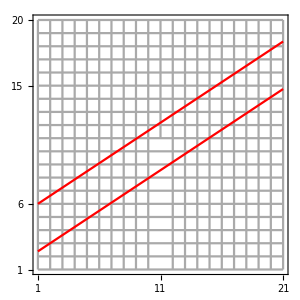

```mathematica
Show[P5,
Plot[LineUp[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+0.1}}],
Plot[LineDn[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+0.1}}],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
ImageSize-> 300,AspectRatio-> 1
]
```

```mathematica
(**---This function generates site number for a given coordinates and set of parameter---**)
```

```mathematica
(**---Generates 0 for non existing points, e.g. the two lines below and above dislocation centers---**)
```

```mathematica
GenerateSiteNumber[x_,y_,Lx_,Ly_,l_,mL_]:=Piecewise[{{x+(y-1)Lx, 1≤ x ≤ mL &&1≤ y≤ l },{x+(y-1)Lx-1, Lx+1≥ x > mL+1 &&1≤ y≤ l},{x+(y-1)(Lx+1)-l,l<y≤Ly&&Lx+1≥ x ≥ 1 }},0]
```

```mathematica
Clear[FibonListNew]
FibonListNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
(**--x runs from 1 to Lx + 1--**)
```

```mathematica
Do[Do[FibonListNew=Append[FibonListNew,GenerateSiteNumber[x,y,Lx,Ly,l,mL]],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx+1}]
```

```mathematica
FibonList=Sort[FibonListNew];
```

```mathematica
(**--Delete the zeros, which are generated for the non-existing lines of atoms (the sites which have been removed) --**)
```

```mathematica
FibonList=DeleteCases[FibonList,0];
```

```mathematica
Dimensions[FibonList]
```

{73}

```mathematica
Clear[Fibonup, Fibondown, TotalFibon]
```

```mathematica
Fibonup = 2 * FibonList -1;
```

```mathematica
Fibondown = 2* FibonList;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon=Sort[TotalFibon];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

146

```mathematica
NOrbitalsQuasi/2
```

73

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

654

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{820}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
Dimensions[a]
```

{674}

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------------------------Create matrices for the Hamiltonian of the projected brane-------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHIDisloc[t,t0,m,1];
```

```mathematica
Clear[ SX2DSingDis,SY2DSingDis,
 CX2DSingDis,CY2DSingDis,
SX2DPSingDis,CX2DPSingDis,
 Cons]
```

```mathematica
(*---------------This is H11-----------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
Clear[Hfbfb]
```

```mathematica
(*---------------This is H22-----------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
Clear[H2d2d]
```

```mathematica
(*------------------This is H21------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
Clear[H2dfb]
```

```mathematica
(*------------------This is H12------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
Clear[Hfb2d]
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon]
```

```mathematica
(** This is the effective Hamiltonian HPTB, defined in Eq. 1 in our paper **)
```

```mathematica
(** Sometimes the inverse does not exist because of a single zero eigenvalue -- we will regularize it **)
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D- 0.000001 IdentityMatrix[NOrbitalsOutside]].H2DFB);
```

```mathematica
(*** To save memory, I delete some matrices which are not required anymore **)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
(**-----------Diagonalize HPTB----------------**)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{Re[ValueFibon],VecFibon}],First];
```

```mathematica
ValFibon=Re[Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]]//Chop;
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ValFibon[[(NOrbitalsQuasi/2)+1,2]]
```

1.06319

```mathematica
(*-----------------------Now we generate the joint LDoS of the two states closest to the zero energy------------------------------------*)
```

```mathematica
(** Put the Local density of states (probability density) corresponding to the two energies closest to zero in a list **)
```

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabDataFibon=Table[{i,0,
Abs[ValVecFibon[[J,2,2i]]]^2+Abs[ValVecFibon[[J,2,2i-1]]]^2

+Abs[ValVecFibon[[J+1,2,2i]]]^2+Abs[ValVecFibon[[J+1,2,2i-1]]]^2
},{i,1,NOrbitalsQuasi/2}];
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]/2},{i,1,3*NOrbitalsQuasi/2,3}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
SiteIndex=Table[{i,0},{i,1,NOrbitalsQuasi/2}];
```

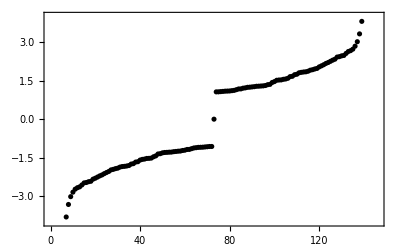

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}]]
```

```mathematica
(** Need to export ValFibon and TabFibonacci **)
```

```mathematica
Export["EigenvaluesParent60DislocationRational10to12mbyt0=6PBC.dat",ValFibon]
```

```mathematica
Export["LDOSParent60DislocationRational10to12mbyt0=6PBC.dat",TabFibonacci]
```

```mathematica
tStop = AbsoluteTime[];
```

```mathematica
timeTakenInSeconds = tStop - tStart
```

16.99593